Finite differences plot of function with boundary at x^2+y^2≥1

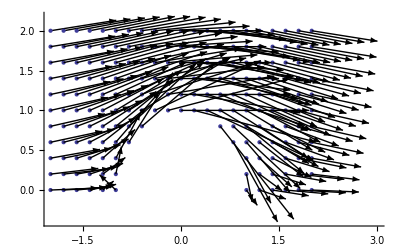

Mean norm vector differences error between gradient and finite differences method: {-0.0000359692,0.0000323722}

```mathematica
Clear[i,x,y,pList,lPlot,arr,ePts]
f[x_,y_]:=x+x/(x^2+y^2);
Δx=.2;
Δy=.2;
arr={};
centralX[x_,y_]:=(f[x+Δx,y]-f[x-Δx,y])/(2*(Δx));
centralY[x_,y_]:=(f[x,y+Δy]-f[x,y-Δy])/(2*(Δx));
forwardX[x_,y_]:=(f[x+Δx,y]-f[x,y])/Δx;
forwardY[x_,y_]:=(f[x,y+Δy]-f[x,y])/Δy;
backwardX[x_,y_]:=(f[x,y]-f[x-Δx,y])/Δx;
backwardY[x_,y_]:=(f[x,y]-f[x,y-Δy])/Δy;
eLine[x_,y_]={x,y}+{centralX[x,y],centralY[x,y]} ;
gradf[x_,y_]:=Evaluate[{D[f[x,y],x],D[f[x,y],y]}];
gLine[x_,y_]={x,y}+gradf[x,y];
ePts={};
i=0;
x=-2.;
pList={};
While[x≤2.,
y=0;
While[y≤2.,
If[x^2+y^2≥1.,
AppendTo[pList,{x,y}];
	If[{x,y}=={-2,0},
(*corners*)
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],forwardY[x,y]});
		i++
	];
	If[{x,y}=={2,0},
	AppendTo[arr,Arrow[{{x,y},{x,y}+{backwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{backwardX[x,y],forwardY[x,y]});
		i++
	];
	If[{x,y}=={-2,2},
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],backwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],backwardY[x,y]});
		i++
	];
	If[{x,y}=={2,2},
	AppendTo[arr,Arrow[{{x,y},{x,y}+{backwardX[x,y],backwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{backwardX[x,y],backwardY[x,y]});
		i++
	];
	(*right side*)
	If[x==2  && (y<2&&y>0),
	AppendTo[arr,Arrow[{{x,y},{x,y}+{backwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{backwardX[x,y],forwardY[x,y]});
		i++
	];
(*top*)
	If[y==2  && (x<2&&x>-2),
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],backwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],backwardY[x,y]});
		i++
	];
(*left side*)
	If[x==-2  && (y<2&&y>0),
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],forwardY[x,y]});
		i++
	];
(*bottom*)
	If[y==0  && (x<2&&x>-2),
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],forwardY[x,y]});
		i++
	];
(*left side of semi circle*)
	If[x^2+y^2==1&&x<0&&y>0,
	AppendTo[arr,Arrow[{{x,y},{x,y}+{backwardX[x,y],forwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{backwardX[x,y],forwardY[x,y]});
		i++
	];
(*right side of semi circle*)
	If[x^2+y^2==1&&x≥0&&y>0,
	AppendTo[arr,Arrow[{{x,y},{x,y}+{forwardX[x,y],backwardY[x,y]}}]];
		ePts=gLine[x,y]-({x,y}+{forwardX[x,y],backwardY[x,y]});
		i++
	];
(*interior*)
	If[x>-2&&x<2&&y<2&&y>0&&x^2+y^2>1,
	AppendTo[arr,Arrow[{{x,y},eLine[x,y]}]];
		ePts=gLine[x,y]-({x,y}+eLine[x,y]);
		i++
	]
];
y+=.2];
x+=.2];
lPlot=ListPlot[pList];
Print["Finite differences plot of function with boundary at x^2+y^2≥1"]
Show[lPlot,Graphics[{Arrowheads[Small],arr}]]
Print["Mean norm vector differences error between gradient and finite differences method: ",ePts/i]
```